```mathematica
SetDirectory[NotebookDirectory[]];

IsIndCopula[Copula_]:=(Copula=== "Product");

GetTestName[Copula_,Margs_]:=Module[{n=Length[Margs]},
If[IsIndCopula[Copula], "Independent",ToString[Copula[[1]]]]<>"_"<>StringTrim[ToString[Margs[[1,0]]],"Distribution"]<>"_"<>ToString[n]<>"_dim"
];

PrintResults[EstNames_,AllEsts_,AllStdDevs_,AllTimes_,AllREs_]:=Module[{},
(* Estimates. *)
Print["Estimates:"];
Do[Print["\t* ", EstNames[[e]],": ", AllEsts[[e]]],{e,Length[AllEsts]}];

(* Standard deviations. *)
Print["Standard deviations:"];
Do[Print["\t* ", EstNames[[e]],": ", AllStdDevs[[e]]],{e,Length[AllStdDevs]}];

(* Computation times. *)
Print["Times:"];
Do[Print["\t* ", EstNames[[e]],": ", AllTimes[[e]]],{e,Length[AllTimes]}];

(* Estimated relative errors. *)
Print["Estimated Relative errors:"];
Do[Print["\t* ", EstNames[[e]],": ", AllREs[[e]]],{e,Length[AllREs]}];
];

PlotResults[TestName_,ss_,EstNames_,AllEsts_,AllStdDevs_,AllTimes_,AllREs_]:=Module[{WithS,Colours,EstimatesPlotSmall,EstimatesPlot,StdDevsPlotSmall,SqrtWNRVPlotSmall,SqrtWNRVPlot,CombinedPlot},

WithS[Data_]:=Transpose[{ss,Data}];
Colours=Lookup["DefaultPlotStyle"]@Lookup[Method]@Charting`ResolvePlotTheme[Automatic,Plot];

EstimatesPlotSmall=
ListPlot[Map[WithS,AllEsts],Joined->True,ImageSize-> {250,125},AspectRatio->1/2,LabelStyle->{FontSize -> 11},PlotStyle->Thickness[0.012],AxesLabel-> {"x","Estimates"}];

EstimatesPlot=
ListPlot[Map[WithS,AllEsts],Joined->True,ImageSize-> {500,125},AspectRatio->0.21,LabelStyle->{FontSize -> 11},PlotStyle->Thickness[0.006],AxesLabel-> {"x","Estimates"}];

StdDevsPlotSmall=
ListPlot[Map[WithS,AllStdDevs],Joined->True,PlotStyle->Thickness[0.012],LabelStyle->{FontSize -> 11},PlotRange->{0,0.76} ,AxesLabel-> {"x","Standard Deviation"},ImageSize->{250,125},AspectRatio->1/2];

SqrtWNRVPlotSmall=
ListPlot[Map[WithS,AllREs],Joined->True,ImageSize->{250,125},LabelStyle->{FontSize -> 11}, AspectRatio->1/2,PlotStyle->Thickness[0.012],AxesLabel-> {"x","Sqrt(WNRV)"},PlotRange->{0,2}];

SqrtWNRVPlot=
ListPlot[Map[WithS,AllREs],Joined->True,ImageSize-> {500,125}, LabelStyle->{FontSize -> 11}, AspectRatio->0.21,PlotStyle->Thickness[0.006],AxesLabel-> {"x","Sqrt(WNRV)"}, PlotRange->{0,2}];

CombinedPlot=Legended[Column[{EstimatesPlot,Row[{SqrtWNRVPlotSmall,StdDevsPlotSmall}]},Center],Placed[LineLegend[Colours,EstNames,LegendLayout->"Row"],Below]];

Print[TestName<>".pdf"];
Print[CombinedPlot];
Export[TestName<>".pdf",CombinedPlot];
];

PrintAndPlotResults[Copula_,Margs_,R_,ss_,PushoutEsts_,PushoutVars_,PushoutTime_,CondEsts_,CondVars_,CondTime_,AKEsts_,AKVars_,AKTime_]:=Module[{TestName,WithS,Colours,EstNames,AllEsts,AllStdDevs,AllTimes,AllREs,EstimatesPlotSmall,StdDevsPlotSmall,SqrtWNRVPlot,SqrtWNRVPlotSmall,CombinedPlot},

TestName= GetTestName[Copula,Margs];

EstNames={"Sensitivity","CondMC", "AK"};
AllEsts={PushoutEsts,CondEsts,AKEsts};
AllStdDevs=Sqrt@{PushoutVars,CondVars,AKVars};
AllTimes={PushoutTime,CondTime,AKTime};
AllREs=Quiet[Sqrt@{(PushoutTime * (PushoutVars/R)/PushoutEsts^2),(CondTime * (CondVars/R)/CondEsts^2),(AKTime * (AKVars/R)/AKEsts^2)},{Power::infy,Infinity::indet}];

PlotResults[TestName,ss,EstNames,AllEsts,AllStdDevs,AllTimes,AllREs];

Print[TestName," done"];
];
```

GumbelHougaard_Exponential_15_dim.pdf

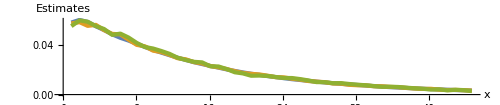
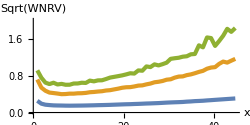
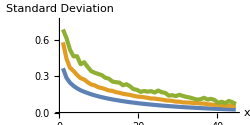

GumbelHougaard_Exponential_15_dim done

```mathematica
(* Test 3: {"GumbelHougaard",5},ExponentialDistribution[1] *)
Copula={"GumbelHougaard",5};
Margs=Table[ExponentialDistribution[1],{i,15}];
R=10^5;
ss={0.8934766871747459,1.7869533743494919,2.6804300615242376,3.5739067486989837,4.46738343587373,5.360860123048475,6.254336810223221,7.1478134973979675,8.041290184572713,8.93476687174746,9.828243558922205,10.72172024609695,11.615196933271697,12.508673620446443,13.40215030762119,14.295626994795935,15.18910368197068,16.082580369145425,16.976057056320172,17.86953374349492,18.763010430669663,19.65648711784441,20.549963805019157,21.4434404921939,22.336917179368648,23.230393866543395,24.12387055371814,25.017347240892885,25.910823928067632,26.80430061524238,27.697777302417123,28.59125398959187,29.484730676766617,30.37820736394136,31.271684051116107,32.16516073829085,33.0586374254656,33.952114112640345,34.84559079981509,35.73906748698984,36.632544174164586,37.526020861339326,38.41949754851407,39.31297423568882,40.20645092286357,41.099927610038314,41.99340429721306,42.8868809843878,43.78035767156255,44.673834358737295};
PushoutEsts={0.05788906500437095,0.05998296194951197,0.0583648534817816,0.05489620283626031,0.05184870228593607,0.04840662478220683,0.04560647952417633,0.04339904098931664,0.04083513899367302,0.03826185563553651,0.035840630519146426,0.033736760675501215,0.03168494213368379,0.0296481290941657,0.027852428759861006,0.02602639933965191,0.024521942563637086,0.023030683148152133,0.021653502967544154,0.02024609537211981,0.01899093914688325,0.017811860126731593,0.016747699997448916,0.015864045302224822,0.014880192093121618,0.014045173935367142,0.0131918148618057,0.012378269552301122,0.011720025057198085,0.011025377116883213,0.010411315696324632,0.009760653727769778,0.009142387738481193,0.008623756647306477,0.008153559216562955,0.0077205197878302155,0.007294117954030904,0.006787633504656322,0.006405608280739776,0.005977788851312956,0.00564981505952761,0.005323465443914376,0.0049724388687664225,0.004676436880023248,0.0043900122576178745,0.004126230585666368,0.0038940474407645202,0.0036630152501731916,0.0034491676719764506,0.0032541703781557604};
CondEsts={0.05718225100012138,0.058181261293623526,0.05523005885882743,0.05600077121212238,0.051811597489392146,0.04877293969720398,0.04838155784076514,0.044102702037217424,0.039941163920428915,0.03877181489847315,0.03530010477258826,0.03413480854722907,0.03196280703135451,0.029240015758395008,0.028341347561851603,0.026109077895041896,0.02494682550190415,0.022958883907440112,0.021884575055645897,0.020546612070845394,0.018820929654253277,0.017431942117365273,0.016656690142597682,0.016190237711077988,0.015202132111786495,0.013992090792506042,0.01384437540465027,0.012739141127140008,0.012001614010023223,0.010891538712346412,0.010438520330030229,0.009968153256215015,0.008929691148578544,0.008780388823237424,0.007833519904896245,0.007500324839119049,0.007408579834281047,0.006699360213075852,0.006687048360282953,0.0061804504581799095,0.005927840499274639,0.005346061746277692,0.004911463143073879,0.004567148966736769,0.0046579978990176985,0.003978842185801702,0.003666127812097609,0.0037821729324184297,0.0035008206303044137,0.0032265012427156615};
AKEsts={0.054979332157595893,0.05962652842329793,0.058545484471733814,0.055029619543189676,0.05271702540890736,0.04799508998537477,0.0489810849039389,0.045827641462342555,0.04152732773830234,0.038220748918423565,0.03702413651932742,0.035037929228336095,0.032771378706543494,0.02961708245359554,0.027778110133289534,0.026328048437402968,0.02589028441353932,0.02271882439775547,0.022595335041718893,0.02052383670946979,0.017925694626004487,0.016998737319166995,0.015139924687047966,0.015281611398115397,0.014939562312220099,0.014146969988134037,0.013346892704747416,0.013295682757153801,0.012444229377649885,0.011382502394669777,0.010009838196486825,0.009987672304573755,0.009161049399193164,0.009221238752456914,0.008511654963673246,0.007968392426045882,0.0074826415775996365,0.0068895855406956195,0.006226333966392805,0.0063135601748914106,0.006108098104866995,0.0055372267245978124,0.005081217282179597,0.0046702164477413904,0.004043270025398358,0.004206580785955808,0.00339601816688758,0.003858994187958884,0.0035903482820250137,0.00280477618459317};

PushoutVars={0.36483651533633826,0.2855986218044926,0.24538240945264087,0.21959387006891315,0.19916874103742166,0.18314885614945764,0.1712039886927997,0.16053355630021646,0.15021528172432583,0.14150987783245117,0.13354798988607527,0.12638445515878752,0.1200092800645404,0.11381218771515988,0.10817287363428629,0.10302057657097495,0.09809342914180272,0.09349994505939652,0.08923808845347814,0.08518084337222709,0.08137586041972156,0.07780440670040488,0.07440465949719817,0.07120763532752654,0.06818916323228302,0.06530835503151153,0.06257782481129417,0.05994476302959007,0.05746494357169955,0.05507308928082358,0.05286079389833969,0.05074140943446713,0.04869022296120601,0.04676577162673832,0.04490595301815826,0.04308760251805563,0.041409498088654954,0.03969066629874696,0.038182753012880974,0.03664180871766355,0.03515767179684236,0.033705452785237434,0.03236500476525613,0.03110904627294585,0.029916538884611397,0.028735196671162703,0.027698192141506234,0.026615745087048913,0.02556612501505188,0.024610487632730375}^2;
CondVars={0.5782209166993388,0.44381083861002296,0.3683361517277099,0.3422576653663534,0.30914670800227523,0.2833050241258577,0.2720822678434435,0.24977833408614905,0.23109204309903839,0.22407920601903702,0.207997927991653,0.2019413292798088,0.19224914656091172,0.18180451854547974,0.17855472607875306,0.16794101353983804,0.1627877100166203,0.1548025213412635,0.1497868804935177,0.14546744357943536,0.13758162283193653,0.1322577809797742,0.1289713110836932,0.1259210536681412,0.12138137993057037,0.115407183222703,0.11520912486285259,0.10992450436930949,0.10649833550157893,0.10092114600617536,0.0983413581559488,0.09632016187415711,0.08977894104783296,0.08941706174867427,0.08368132738553626,0.08257519772640425,0.08198865017664507,0.07677011590179007,0.07812101961486413,0.07439330658519656,0.07375109067540785,0.06824029525594506,0.06591095002147553,0.06291575194171811,0.06476164593095796,0.059295923904281296,0.057204981726683445,0.05783734603052473,0.055586639924148966,0.053030360326755586}^2;
AKVars={0.6847585226874779,0.6133409102849903,0.5168392617448324,0.4628049307797177,0.4639158730001708,0.3980252370456643,0.41436353311207347,0.37583072503943293,0.34112016071711426,0.32747787700776915,0.3178680394784198,0.308312922992098,0.2865094030513795,0.2790658047213159,0.2558014032045691,0.24996097969548917,0.2466246916113819,0.22481110108740582,0.23315125683874668,0.2161764715484664,0.192652955657419,0.18656130545450714,0.17055961018851037,0.17722198275312143,0.17191668651942146,0.1758917582812523,0.16482150849082614,0.1810358177270997,0.1670828063746526,0.16192461839863365,0.1393271666333688,0.14269436860066748,0.1348612024306851,0.1462306511022566,0.13648805244686646,0.12892318309930967,0.1234222715749392,0.1145113980113585,0.10708577327028665,0.1091704032829,0.12121076872560362,0.10663756325021824,0.11269444450796012,0.10272702297589009,0.07954080090103999,0.08881551170574971,0.07701730349589037,0.09539702502708436,0.08556906752811681,0.0700051329280071}^2;

PushoutTime=162.866;
CondTime=501.151;
AKTime=538.903;

PrintAndPlotResults[Copula,Margs,R,ss,PushoutEsts,PushoutVars,PushoutTime,CondEsts,CondVars,CondTime,AKEsts,AKVars,AKTime]
```